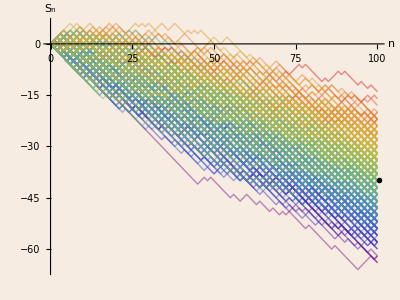

/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/asymmetric_left_random_walks_1d_hist.svg

```mathematica
Options[svgExport]={"CommentString"->"Created by Mathematica",AspectRatio->Automatic,Background->Automatic};
Clear[svgExport];
svgExport[name_String,gr_,opts:OptionsPattern[]]:=Module[{svgCode=StringReplace[ExportString[First@ImportString[ExportString[gr,"PDF",Background->OptionValue[Background]],"PDF"],"SVG",Background->OptionValue[Background]],"<svg "->"<svg "<>If[OptionValue[AspectRatio]===Full," preserveAspectRatio='none' "," "]]&[ToString/@ImageDimensions[Rasterize[Show[gr,ImagePadding->0],"Image"]]]},Export[name,StringReplace[svgCode,RegularExpression["(<svg\\b[^>]*>)"]:>"$1"<>"\n<!-- ***Exported Comment***\n"<>OptionValue["CommentString"]<>"\n***Exported Comment*** -->"],"Text"]]

SeedRandom[1234];
data=RandomFunction[RandomWalkProcess[.3],{100},500];
sd=data["SliceData",100];
cf=ColorData["Rainbow"];sliced=BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{Min[sd],Max[sd]},{0,1}]),ImageSize->60]&[HistogramList[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/15]}]];
plot = ListLinePlot[data,ImageSize->400,PlotRange->All,AspectRatio->3/4,
Background->RGBColor[247/255,236/255,226/255], AxesLabel->{HoldForm[n],HoldForm[Subscript[S,n]]},Epilog->Inset[sliced,{100.5,Mean[sd]},{0,8}],PlotStyle->(cf/@Rescale[sd]),
BaseStyle->Directive[Thin,Opacity[0.5]],AxesStyle->Opacity[1], PlotRangePadding->{{0,20},{.5,7}}]

svgExport["/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/asymmetric_left_random_walks_1d_hist.svg",plot, AspectRatio->Full]
```

-Graphics3D-

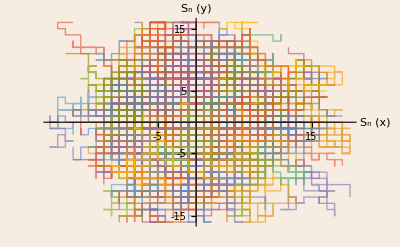

```mathematica
(*2d Random walk*)
Make3d[plot_,height_,opacity_]:=Module[{newplot},newplot=First@Graphics[plot];
newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}:>{x,y,height};
newplot/.GraphicsComplex[xx__]:>{Opacity[opacity],GraphicsComplex[xx]}]

steps = 100;
numwalks = 500;
Randomwalk[n_]:=NestList[#+RandomChoice[{{1,0},{-1,0},{0,1},{0,-1}}]&,{0,0},n]
RandomwalkFixedSlice[n_] := Randomwalk[steps][[steps,All]]
RandomwalkFixed[n_] := Randomwalk[steps]
walks = Array[RandomwalkFixed, numwalks];
GetData[n_] := walks[[n,steps, All]];
slices = Array[GetData, numwalks];
hist = Histogram3D[slices, ChartStyle->Directive[White, Opacity[.4]],Axes->{False, False, False},LabelStyle->(FontFamily->"PT Sans")];
lp = ListLinePlot[walks, BaseStyle->Directive[Thin,Opacity[0.65]],AxesLabel->{HoldForm[Subscript[S,n]"(x)"],HoldForm[Subscript[S,n]"(y)"]},Background->RGBColor[247/255,236/255,226/255],LabelStyle->(FontFamily->"PT Sans"),
Ticks->{Range[-25,25,10]}];
Show[{Graphics3D[Make3d[lp,0,.75], ImageSize->400],hist},Axes->True, Boxed->False,Background->RGBColor[247/255,236/255,226/255], AxesLabel->{HoldForm[Subscript[S,n]"(x)"],HoldForm[Subscript[S,n]"(y)"],""}]
lp
```

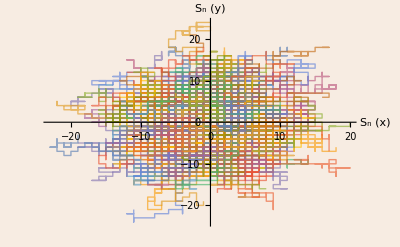

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/symmetric_random_walks_2d_hist.svg",-Graphics3D-, AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/symmetric_random_walks_2d_hist.svg

```mathematica
$FontFamilies
```

{Al Bayan,Alegreya SC,Al Nile,Al Tarikh,American Typewriter,Andale Mono,Apple Braille,Apple Chancery,Apple Color Emoji,AppleGothic,AppleMyungjo,Apple SD Gothic Neo,Apple Symbols,Arial,Arial Black,Arial Hebrew,Arial Hebrew Scholar,Arial Narrow,Arial Rounded MT Bold,Arial Unicode MS,Athelas,Avenir,Avenir Next,Avenir Next Condensed,Ayuthaya,Baghdad,Bangla MN,Bangla Sangam MN,Baskerville,Beirut,Big Caslon,Bitstream Vera Sans Mono,Bodoni 72,Bodoni 72 Oldstyle,Bodoni 72 Smallcaps,Bodoni Ornaments,Bradley Hand,Brush Script MT,Chalkboard,Chalkboard SE,Chalkduster,Charter,Clear Sans,Clear Sans Light,Clear Sans Medium,Clear Sans Thin,Cochin,Comic Sans MS,Copperplate,Corsiva Hebrew,Courier,Courier New,Cousine,Damascus,DecoType Naskh,Devanagari MT,Devanagari Sangam MN,Didot,DIN Alternate,DIN Condensed,Diwan Kufi,Diwan Thuluth,Droid Serif,EB Garamond,EB Garamond 12 All SC,EB Garamond SC,Economica,Euphemia UCAS,Farah,Farisi,Felipa,Futura,Galvji,GB18030 Bitmap,Geeza Pro,Geneva,Gentium Basic,Georgia,Gill Sans,Gujarati MT,Gujarati Sangam MN,Gurmukhi MN,Gurmukhi MT,Gurmukhi Sangam MN,Hack Nerd Font,Heiti SC,Heiti TC,Helvetica,Helvetica Neue,Herculanum,Hiragino Kaku Gothic Pro,Hiragino Kaku Gothic ProN,Hiragino Kaku Gothic Std,Hiragino Kaku Gothic StdN,Hiragino Maru Gothic Pro,Hiragino Maru Gothic ProN,Hiragino Mincho Pro,Hiragino Mincho ProN,Hiragino Sans,Hiragino Sans GB,Hoefler Text,Impact,InaiMathi,Inconsolata,Iowan Old Style,ITF Devanagari,ITF Devanagari Marathi,Kailasa,Kalam,Kannada MN,Kannada Sangam MN,Kefa,Khmer MN,Khmer Sangam MN,Kohinoor Bangla,Kohinoor Devanagari,Kohinoor Gujarati,Kohinoor Telugu,Kokonor,Krungthep,KufiStandardGK,Lao MN,Lao Sangam MN,Lato,League Gothic,Lucida Grande,Luminari,Malayalam MN,Malayalam Sangam MN,Marion,Marker Felt,Menlo,Microsoft Sans Serif,Mishafi,Mishafi Gold,Monaco,Mshtakan,Mukta Mahee,Muna,Myanmar MN,Myanmar Sangam MN,Nadeem,New Peninim MT,Noteworthy,Noto Nastaliq Urdu,Noto Sans Armenian,Noto Sans Avestan,Noto Sans Bamum,Noto Sans Batak,Noto Sans Brahmi,Noto Sans Buginese,Noto Sans Buhid,Noto Sans Carian,Noto Sans Chakma,Noto Sans Cham,Noto Sans Coptic,Noto Sans Cuneiform,Noto Sans Cypriot,Noto Sans Egyptian Hieroglyphs,Noto Sans Glagolitic,Noto Sans Gothic,Noto Sans Hanunoo,Noto Sans Imperial Aramaic,Noto Sans Inscriptional Pahlavi,Noto Sans Inscriptional Parthian,Noto Sans Javanese,Noto Sans Kaithi,Noto Sans Kannada,Noto Sans Kayah Li,Noto Sans Kharoshthi,Noto Sans Lepcha,Noto Sans Limbu,Noto Sans Linear B,Noto Sans Lisu,Noto Sans Lycian,Noto Sans Lydian,Noto Sans Mandaic,Noto Sans Meetei Mayek,Noto Sans Mongolian,Noto Sans Myanmar,Noto Sans New Tai Lue,Noto Sans NKo,Noto Sans Ogham,Noto Sans Ol Chiki,Noto Sans Old Italic,Noto Sans Old Persian,Noto Sans Old South Arabian,Noto Sans Old Turkic,Noto Sans Oriya,Noto Sans Osmanya,Noto Sans PhagsPa,Noto Sans Phoenician,Noto Sans Rejang,Noto Sans Runic,Noto Sans Samaritan,Noto Sans Saurashtra,Noto Sans Shavian,Noto Sans Sundanese,Noto Sans Syloti Nagri,Noto Sans Syriac,Noto Sans Tagalog,Noto Sans Tagbanwa,Noto Sans Tai Le,Noto Sans Tai Tham,Noto Sans Tai Viet,Noto Sans Thaana,Noto Sans Tifinagh,Noto Sans Ugaritic,Noto Sans Vai,Noto Sans Yi,Noto Sans Zawgyi,Noto Serif Balinese,Noto Serif Myanmar,Optima,Oriya MN,Oriya Sangam MN,Oswald,Palatino,Papyrus,Phosphate,PingFang HK,PingFang SC,PingFang TC,Plantagenet Cherokee,Playfair Display,PT Mono,PT Sans,PT Sans Caption,PT Sans Narrow,PT Serif,PT Serif Caption,Raanana,Roboto,Roboto Condensed,Roboto Slab,Rockwell,Sana,Sathu,Savoye LET,Seravek,Shadows Into Light Two,Shree Devanagari 714,SignPainter,Silom,Sinhala MN,Sinhala Sangam MN,Skia,Snell Roundhand,Songti SC,Songti TC,Source Code Pro,Source Sans Pro,Source Serif Pro,STIXGeneral,STIXIntegralsD,STIXIntegralsSm,STIXIntegralsUp,STIXIntegralsUpD,STIXIntegralsUpSm,STIXNonUnicode,STIXSizeFiveSym,STIXSizeFourSym,STIXSizeOneSym,STIXSizeThreeSym,STIXSizeTwoSym,STIXVariants,STSong,Sukhumvit Set,Superclarendon,Symbol,Tahoma,Tamil MN,Tamil Sangam MN,Telugu MN,Telugu Sangam MN,Thonburi,Times,Times New Roman,Titillium Web,Trattatello,Trebuchet MS,Verdana,Waseem,Webdings,Wingdings,Wingdings 2,Wingdings 3,Yanone Kaffeesatz,Zapf Dingbats,Zapfino}